## B-Spline Curves

Our B-spline curves are made up with cubic B-spline functions based on the integer knots.  First we construct cubic B-splines.

## Cubic B-splines

Let B(x)=B_3(x) denote the cubic B-spline that has support set on [0, 4], which is defined inductively by
         B_0(x) = 1, if x in [0,1], and B_0(x) = 0 if x is outside [0,1],
         B_1(x) =  x B_0(x) + (2- x) B_0(x -1),  and    B_2(x) = x/2 B_2(x) + (3-x)/2 B_2(x -1),  and finally
        B(x) = x/3 B_2(x) + (4-x)/3 B_2(x -1). 
Other B-splines based on the integer knots are just translations of B(x). For example, the cubic B-spline that has the support set [n, n+4] is  B(x - n).

```mathematica
B0[x_] = If[ 0<= x && x <1, 1,0];   
   B1[x_] = If[0 <= x  && x <2, x B0[x]+ (2-x) B0[x-1], 0];  
   B2[x_] = If[0 <= x  && x <3, x B1[x]/2+(3-x) B1[x-1]/2, 0];  
   B3[x_] = If[0 <= x  && x <4, x B2[x]/3+(4-x) B2[x-1]/3, 0];
```

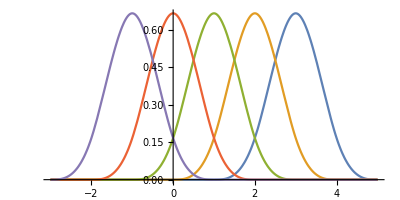

```mathematica
Plot[{B3[x-1],B3[x],B3[x+1], B3[x+2], B3[x+3]}, {x, -3,5}, AspectRatio->0.5]
```

## Cubic B-spline curves (first attempt)

In order to use B-splines to draw a curve, we consider B-splines with non-zero support on [0,1] with the knots t_i = i/n, i= 0,1,... n.  The B-splines based on these knots are then B(n(t- t_i)) = B(nt - i). 

Given a sequence of "control points" XY = {(x_0, y_0), (x_1, y_1) ..., (x_n, y_n)}, the simplest way to construct a B-spline curve is using 
                 B(t) =  ∑_(i=1)^n  XY[i]B3[nt-i+2]                           
Note that B(t) is actually a vector. We call its x component BX(t) and its y component BY(t). Then B(t) = (BX(t), BY(t)) gives the parametric form of the curve.

### Algorithm

```mathematica
Bspline[XY0_,t_] := Block[{n,XY},
XY = XY0; n = Length[XY]; 
B[t]= Sum[XY[[i]]B3[n*t-i+2],{i,n}];
Return[B[t]]; ];
```

To use the algorithm, all it needs is to have a given set of data XY in the form of  XY ={(x_0, y_0), (x_1, y_1) ..., (x_n, y_n)}, then run   
            Bspline[XY, t]  
 The two components of the spline are given by 
            BX[t_] = B[t][[1]];  BY[t_] = B[t][[2]];

### Example

Example 1.

```mathematica
XY = {{0.,0.2},{1.,0.},{2.,0.2}, {3.,1.},{4.,1.3},{5.,1.3}, {6.,1.}, {5.,0.8}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

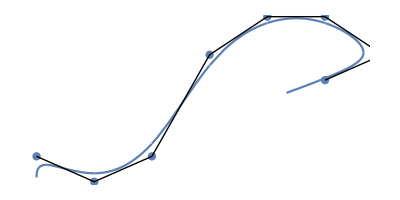

```mathematica
dots = ListPlot[XY, PlotStyle->{PointSize[0.015]},DisplayFunction->Identity];
gr = ParametricPlot[{BX[t],BY[t]},{t,0,1},AspectRatio ->0.5, DisplayFunction->Identity];
Show[gr,dots,Graphics[Line[XY]],DisplayFunction->$DisplayFunction, Axes->False]
```

Example 2. Script D:

```mathematica
XY = {{-1,4},{-0.8,0},{-1.5,-6},{-1.8,-5}, {-1.5,-3},{-0.5,-5},{0,-4},{0.7,2}, {0,7},{-1,8},{-1.5,2},{0,-8}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

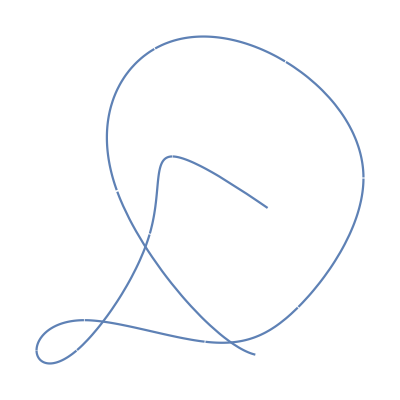

```mathematica
curve=ParametricPlot[{BX[t],BY[t]},{t,0,1}, Axes->False,AspectRatio ->1]
```

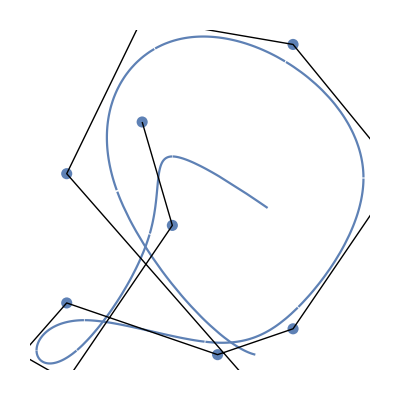

```mathematica
nodes=ListPlot[XY,Frame->False,Axes->False, PlotStyle->PointSize[.02],DisplayFunction->Identity]; 
Show[curve,nodes,Graphics[Line[XY]], 
DisplayFunction->$DisplayFunction]
```

## Discussion

Note that these curve have problems at the end points. This happens because the sum ∑_(i=1)^n  B3[nt-i+2] = 1 does not hold near the end point. To overcome this problem, we need to introduce boundary splines in the following.

## Cubic B-spline with support in [0,1]

We need all B-splines that do not vanish on the interval [0,1]. There are, however, several spline functions that do not vanish on [0,1] but their support sets are not entirely in [0,1]. To keep all support inside, we make up several boundary B-spine pieces that uses repeated knots. These are denoted as C[x] in the following. For example C3[x] is based on the knots 0, 0, 1, 2, 3.

```mathematica
C3[x_] = (1-x)^3 B0[x];
C2[x_] = x(1-x)(2-3x/2) B0[x]+(2-x)^2 B1[x]/4;
C1[x_] = x^2(1-x)B0[x]/2 + x(2-x)B1[x]/4 + (3-x)B2[x]/3;
```

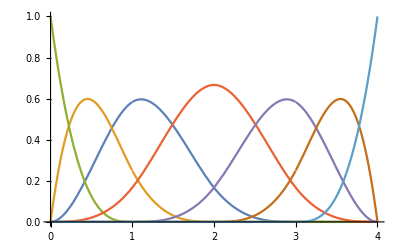

```mathematica
Plot[{C1[x],C2[x], C3[x], B3[x], C1[4-x],C2[4-x], C3[4-x]}, {x, 0,4}]
```

## Cubic B-spline curves

Given a sequence of "control points" XY = {(x_0, y_0), (x_1, y_1) ..., (x_n, y_n)}, the B-spline curve is given by  
                 B(t) =XY[1]C3[n t]+XY[2] C2[n t]+ XY[3] C1[nt] + ∑_(i=1)^(n-3)  XY[i+3]B3[nt-i+1]
                           + XY[n+1]C1[n-nt]+XY[n+2]C2[n-nt]+ XY[n+3]C3[n-nt]
Note that B(t) is actually a vector. We call its x component BX(t) and its y component BY(t). Then B(t) = (BX(t), BY(t)) gives the parametric form of the curve.

### Algorithm

```mathematica
Bspline[XY0_,t_] := Block[{n,XY},
XY = XY0; n = Length[XY]-3; 
B[t]= XY[[1]]C3[n*t]+XY[[2]]C2[n*t]+ XY[[3]]C1[n*t]+
 Sum[XY[[i+3]]B3[n*t-i+1],{i,n-3}]+ XY[[n+1]]C1[n-n*t]+XY[[n+2]]*C2[n-n*t]+ XY[[n+3]]C3[n-n*t];
Return[B[t]]; ];
```

To use the algorithm, all it needs is to have a given set of data XY in the form of  XY ={(x_0, y_0), (x_1, y_1) ..., (x_n, y_n)}, then run   
            Bspline[XY, t]  
 The two components of the spline are given by 
            BX[t_] = B[t][[1]];  BY[t_] = B[t][[2]];

### Example

Example 1.

```mathematica
XY = {{0.,0.2},{1.,0.},{2.,0.2}, {3.,1.},{4.,1.3},{5.,1.3}, {6.,1.}, {5.,0.8}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

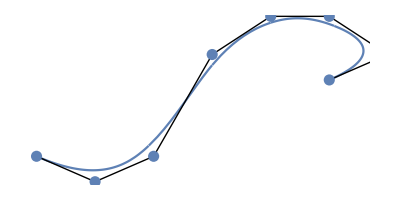

```mathematica
dots = ListPlot[XY,PlotStyle->{PointSize[0.02]},DisplayFunction->Identity];
gr = ParametricPlot[{BX[t],BY[t]},{t,0,1},AspectRatio ->0.5, DisplayFunction->Identity];
Show[gr,Graphics[Line[XY]],dots,DisplayFunction->$DisplayFunction, Axes->False]
```

Example 2. Script D:

```mathematica
XY = {{-1,4},{-0.8,0},{-1.5,-6},{-1.8,-5}, {-1.5,-3},{-0.5,-5},{0,-4},{0.5,2}, {0,7},{-1,8},{-1.5,2},{0,-8}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

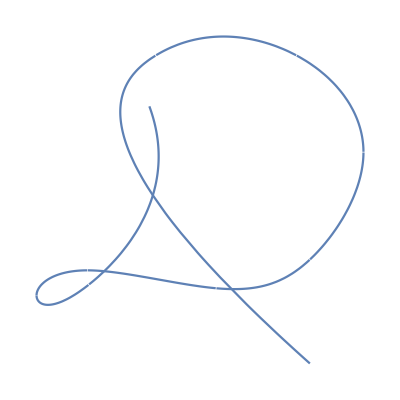

```mathematica
curve=ParametricPlot[{BX[t],BY[t]},{t,0,1}, Axes->False,AspectRatio ->1]
```

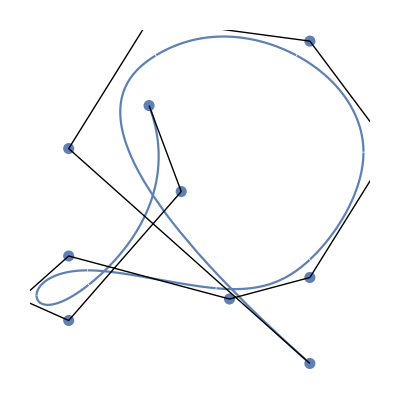

```mathematica
nodes=ListPlot[XY,Frame->False,Axes->False, PlotStyle->PointSize[.02],DisplayFunction->Identity]; 
Show[curve,nodes,Graphics[Line[XY]], 
DisplayFunction->$DisplayFunction]
```

Example 3.  Car: .

```mathematica
XY = {{0.,0.}, {1.2,1.2}, {8.,1.2},{10.,4.},{15.,4},{20.,4.},{22.,2},{27.5,2.},{28.,0}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

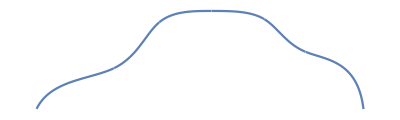

```mathematica
curve=ParametricPlot[{BX[t],BY[t]},{t,0,1}, Axes->False,AspectRatio->0.3]
```

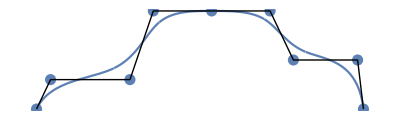

```mathematica
nodes=ListPlot[XY,Frame->False,Axes->False, AspectRatio->0.3,PlotStyle->
PointSize[.02], DisplayFunction->Identity]; 
Show[curve,nodes, Graphics[Line[XY]], DisplayFunction->$DisplayFunction]
```

Example 4.  Duck head:

```mathematica
XY = {{4,-0.5},{3.6,0},{3.25,0},{3.2,0.1}, {3.25,0.2},{3.6,0.3},{3.75,1.2},{4.1,1.3}, {4.5,0},{4.,-0.5}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

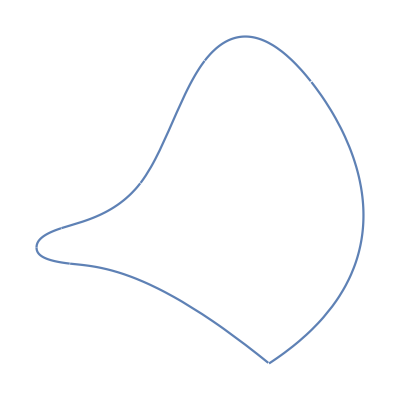

```mathematica
curve=ParametricPlot[{BX[t],BY[t]},{t,0,1}, Axes->False,AspectRatio ->1]
```

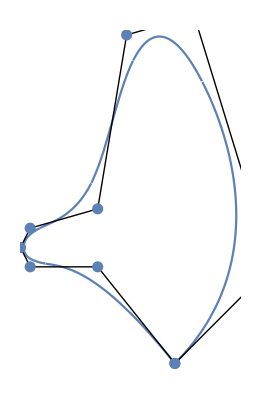

```mathematica
dots = ListPlot[XY,PlotStyle->{PointSize[0.02]},DisplayFunction->Identity];
gr = ParametricPlot[{BX[t],BY[t]},{t,0,1},DisplayFunction->Identity];
Show[gr,Graphics[Line[XY]],dots,DisplayFunction->$DisplayFunction, Axes->False]
```

## Discussion

In the last example, what we have is a closed curve for which (x_0, y_0) = (x_n, y_n). The curve shows a sharp point at bottom. For closed curve, we should use only B[nt - j], but use them for the data {(x_0, y_0), (x_1, y_1), ..., (x_n, y_n),(x_1, y_1), (x_2, y_2)}, in which the last three points are recirculated. This makes a periodic spline.

## Closed cubic B-spline curves:

Given a sequence of “control points” XY = {(x_0, y_0), (x_1, y_1) ..., (x_n, y_n)} such that (x_0, y_0) = (x_n, y_n), the B-spline curve is given by  
        B(t) = XY[0]B3[nt+2]+∑_(i=1)^(n-1)  XY[i]B3[nt-i+2] +XY[0]B3[nt-(n-2)]+XY[1]B3[nt- (n-1)]+XY[2]B3[nt-n]                      
Again B(t) is a vector. We call its x component BX(t) and its y component BY(t). Then B(t) = (BX(t), BY(t)) gives the parametric form of the curve.

### Algorithm

```mathematica
Bspline[XY0_,t_] := Block[{n,XY},
XY = XY0; n = Length[XY]; 
B[t]=XY[n]B3[n*t+2]+ Sum[XY[[i]]B3[n*t-i+2],{i,1,n}]+XY[1]B3[n*t-n+1]+XY[2]B3[n*t-n];
Return[B[t]]; ];
```

To use the algorithm, all it needs is to have a given set of data XY in the form of  XY ={(x_0, y_0), (x_1, y_1) ..., (x_n, y_n)}, then run   
            Bspline[XY, t]  
 The two components of the spline are given by 
            BX[t_] = B[t][[1]];  BY[t_] = B[t][[2]];

### Example

Example 1.  A circle: .

```mathematica
n=10;
XY=Table[{Cos[ 2 k Pi/n], Sin[2 k Pi/n]}, {k,0,n + 3}];B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

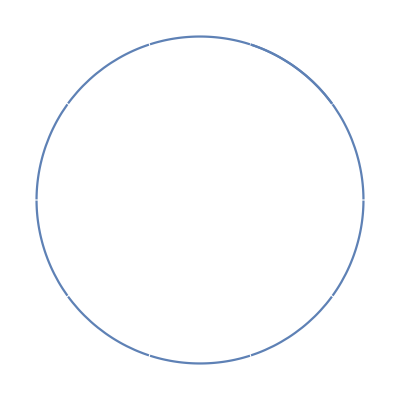

```mathematica
curve=ParametricPlot[{BX[t],BY[t]},{t,-0.1,1.1}, Axes->False,AspectRatio ->1]
```

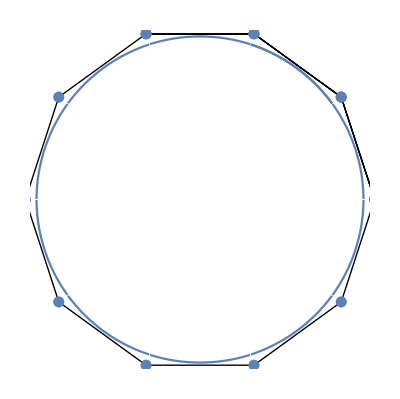

```mathematica
dots = ListPlot[XY,PlotStyle->{PointSize[0.02]},DisplayFunction->Identity];
gr = ParametricPlot[{BX[t],BY[t]},{t,0,1},DisplayFunction->Identity];
Show[gr,Graphics[Line[XY]],dots,DisplayFunction->$DisplayFunction, Axes->False]
```

Example 2.  Duck head: .

```mathematica
XY = {{7.200000000000003,7.},{3.3500000000000014,10.},{-7.05,6.400000000000002},{-11.1,-8.6},{2.0500000000000007,-6.5},{9.200000000000003,9.8},{7.25,3.700000000000001},{6.950000000000003,-13.1},{15.25,-0.8000000000000007}};  
B[t_] = Bspline[XY,t]; 
BX[t_] = B[t][[1]]; 
BY[t_] = B[t][[2]];
```

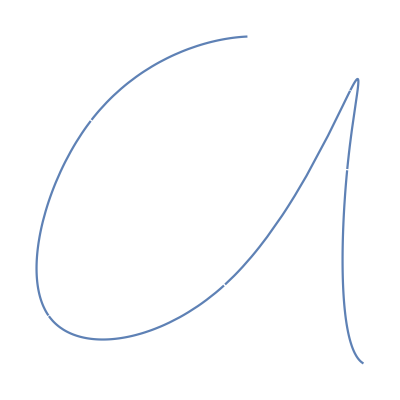

```mathematica
curve=ParametricPlot[{BX[t],BY[t]},{t,0,1}, Axes->False,AspectRatio ->1]
```

Mathematica

Below is the demonstration using Mathematica function: BSplineCurve[ ]

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{5,2},{6,-1},{7,3}};
Graphics[{BSplineCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

-Graphics-

```mathematica
Manipulate[Graphics[{Yellow,Blue,Thick,BSplineCurve[pts,SplineDegree->4],FaceForm[],EdgeForm[{Dashed,Red}],Polygon[pts]},Frame->True,PlotRange->10],{{pts,{{-11.75,10.399999999999999}}},Automatic,ControlType->Locator,LocatorAutoCreate->True},"Alt+click to add points"]
```